```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["../lib/lib2.m"];
Get["../lib/util.m"];
```

```mathematica
changeNK[9, 9];
```

```mathematica
rho[λ_] := 1/($N √(2π))Exp[-λ^2/2]Sum[1/(2^j j!)HermiteH[j, λ/(√2)]^2, {j, 0, $N-1}];
```

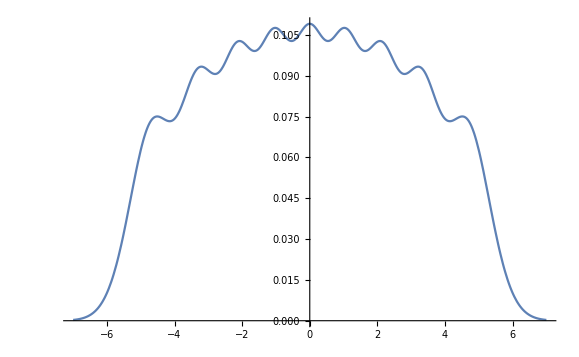

```mathematica
plt = Plot[rho[λ], {λ, -7, 7}]
```

```mathematica
mats = RandomVariate[GaussianUnitaryMatrixDistribution[$N], 100000];
```

```mathematica
eig = Flatten[Eigenvalues/@mats];
```

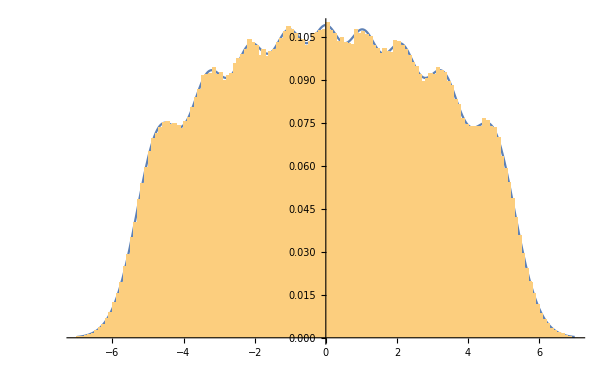

```mathematica
Show[plt, Histogram[eig, 200, PDF]]
```

```mathematica
($N)/(√(2π))Integrate[rho[y]Exp[1/4(λ-y)^2], {y, -∞, ∞}]
```

1/(40320 √π)ⅇ^(λ^2/2) (101206665+482040720 λ^2+339561180 λ^4+82766880 λ^6+9070110 λ^8+497616 λ^10+14028 λ^12+192 λ^14+λ^16)

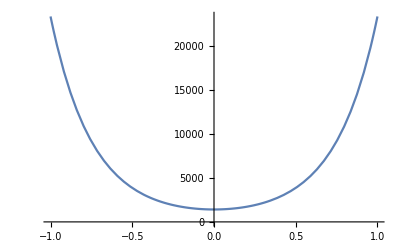

```mathematica
plt = Plot[%46, {λ, -1, 1}]
```

```mathematica
trLessMats = (#-1/($N)Tr[#]IdentityMatrix[$N])&/@mats;
```

```mathematica
trLesseig = Flatten[Eigenvalues/@trLessMats];
```

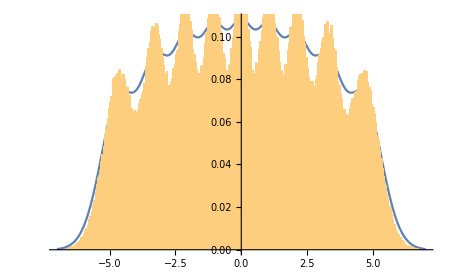

```mathematica
Show[plt, Histogram[trLesseig, 400, PDF]]
```